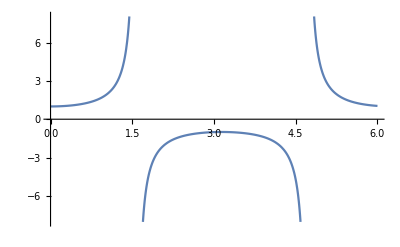

```mathematica
Plot[Sec[x],{x,0,6}]
```

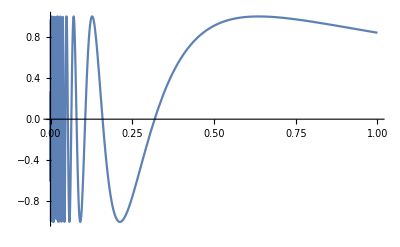

```mathematica
Plot[Sin[1/x],{x,0,1}]
```

```mathematica
Plot3D[Im[Sec[x+I y]],{x,-3,3},{y,-3,3},Lighting->True]
```

-Graphics3D-

```mathematica
? ViewPoint
```

ViewPoint is an option for Graphics3D and related functions which gives the point in space from which three-dimensional objects are to be viewed.

```mathematica
Show[%%,ViewPoint->{4,5,-7}]
```

-Graphics3D-

```mathematica
<<Polyhedra.m
Show[Graphics3D[
Dodecahedron[]]]
```

Get::noopen: Cannot open Polyhedra.m.

$Failed

-Graphics3D-

```mathematica
fac[1]=1
```

1

```mathematica
fac[n_]:=n fac[n-1]
```

```mathematica
fac[2]
```

2

```mathematica
fac[3]
```

6

```mathematica
fac[20]
```

2432902008176640000

```mathematica
?fac
```

Global`fac

fac[1]=1
 
fac[n_]:=n fac[n-1]

```mathematica
log[a b^2 c^3]
```

log[a b^2 c^3]

```mathematica
log[x_ y_]:=log[x]+log[y]
```

```mathematica
log[x_^n_]:=n log[x]
```

```mathematica
log[1 2^2]
```

log[4]

```mathematica
Expand[(x+y)^3/z]
```

x^3/z+(3 x^2 y)/z+(3 x y^2)/z+y^3/z

```mathematica
TeXForm[%]
```

\frac{x^3}{z}+\frac{3 x^2 y}{z}+\frac{3 x y^2}{z}+\frac{y^3}{z}

```mathematica
FortranForm[%]
```

x**3/z + (3*x**2*y)/z + (3*x*y**2)/z + y**3/z

```mathematica
Table["hepple",9]
```

{hepple,hepple,hepple,hepple,hepple,hepple,hepple,hepple,hepple}

```mathematica
Table[n,{n,9}]
```

{1,2,3,4,5,6,7,8,9}

```mathematica
PieChart[{1,1,1,2}]
```

-Graphics-

```mathematica
Table[PieChart[{1,2,3}],3]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Column[Range[n]],{n,10}]
```

{1,1
2,1
2
3,1
2
3
4,1
2
3
4
5,1
2
3
4
5
6,1
2
3
4
5
6
7,1
2
3
4
5
6
7
8,1
2
3
4
5
6
7
8
9,1
2
3
4
5
6
7
8
9
10}

```mathematica
Table[Range[n],{n,10}]
```

{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5},{1,2,3,4,5,6},{1,2,3,4,5,6,7},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8,9,10}}

```mathematica
Table[x-x^2,{x,0,1,.02}]
```

{0.,0.0196,0.0384,0.0564,0.0736,0.09,0.1056,0.1204,0.1344,0.1476,0.16,0.1716,0.1824,0.1924,0.2016,0.21,0.2176,0.2244,0.2304,0.2356,0.24,0.2436,0.2464,0.2484,0.2496,0.25,0.2496,0.2484,0.2464,0.2436,0.24,0.2356,0.2304,0.2244,0.2176,0.21,0.2016,0.1924,0.1824,0.1716,0.16,0.1476,0.1344,0.1204,0.1056,0.09,0.0736,0.0564,0.0384,0.0196,0.}

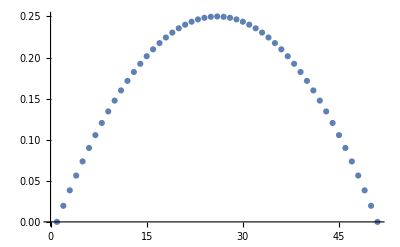

```mathematica
ListPlot[%]
```

```mathematica
Table[x/(x+1),{x,0,10,.1}]
```

{0.,0.0909091,0.166667,0.230769,0.285714,0.333333,0.375,0.411765,0.444444,0.473684,0.5,0.52381,0.545455,0.565217,0.583333,0.6,0.615385,0.62963,0.642857,0.655172,0.666667,0.677419,0.6875,0.69697,0.705882,0.714286,0.722222,0.72973,0.736842,0.74359,0.75,0.756098,0.761905,0.767442,0.772727,0.777778,0.782609,0.787234,0.791667,0.795918,0.8,0.803922,0.807692,0.811321,0.814815,0.818182,0.821429,0.824561,0.827586,0.830508,0.833333,0.836066,0.83871,0.84127,0.84375,0.846154,0.848485,0.850746,0.852941,0.855072,0.857143,0.859155,0.861111,0.863014,0.864865,0.866667,0.868421,0.87013,0.871795,0.873418,0.875,0.876543,0.878049,0.879518,0.880952,0.882353,0.883721,0.885057,0.886364,0.88764,0.888889,0.89011,0.891304,0.892473,0.893617,0.894737,0.895833,0.896907,0.897959,0.89899,0.9,0.90099,0.901961,0.902913,0.903846,0.904762,0.90566,0.906542,0.907407,0.908257,0.909091}

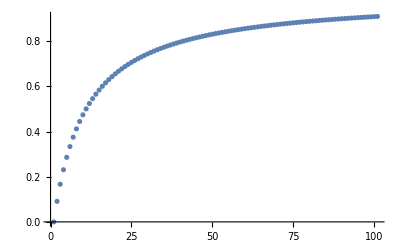

```mathematica
ListPlot[%]
```

```mathematica
RandomInteger[10]
```

1

```mathematica
RandomInteger[10]
```

10

```mathematica
Prime[0]
```

Prime::intpp: Positive integer argument expected in Prime[0].

Prime[0]

```mathematica
Prime[1]
```

2

```mathematica
Length[{2,3,4}]
```

3

```mathematica
Table[1,n]
```

Table::iterb: Iterator {n} does not have appropriate bounds.

Table[1,{n}]

```mathematica
Table[Table[1,n],{n,10}]
```

{{1},{1,1},{1,1,1},{1,1,1,1},{1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1}}

```mathematica
Row[Table[PieChart[Table[1,n]],{n,10}]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

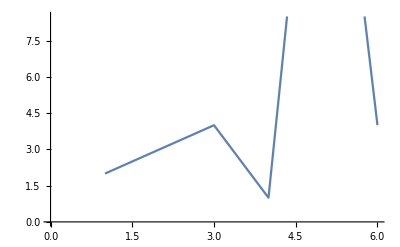

```mathematica
ListLinePlot[{2,3,4,1,23,4}]
```

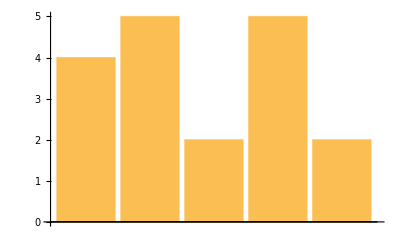

```mathematica
BarChart[{4,5,2,5,2}]
```

```mathematica
PieChart3D[{1,3,41,2,3,1,}]
```

```mathematica
-Graphics3D-
?Row
```

-Graphics3D-

Row[{expr_1,expr_2,…}] is an object that formats with the expr_i arranged in a row, potentially extending over several lines. 
Row[list,s] inserts s as a separator between successive elements.

```mathematica
√(12+3)
```

√15